```mathematica
FormFunction["string"->"String",Style[StringReverse[#string],50]&]
```

FormFunction[]

```mathematica
FormPage["n"->"Integer",Graphics[Style[RegularPolygon[#n],RandomColor[]]]&]
```

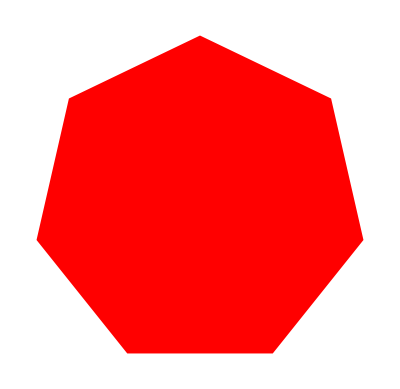

```mathematica
Graphics[Style[RegularPolygon[RandomInteger[{3,8}]],Red]]
```

```mathematica
RandomInteger[{3,8}]
```

7

```mathematica
FormPage[{"location"->"Location", "n"->"Integer"},GeoListPlot[GeoNearest["Volcano",#location,#n]]&]
```

```mathematica
FormPage[{"x"->"String", "y"->"String"},Interpreter["SemanticNumber"][#x]^Interpreter["SemanticNumber"][#y]&]
```

```mathematica
If[EvenQ[#],Style[#,Background->Yellow],Style[#,Background->LightGray]]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
If[PrimeQ[#],Labeled[Framed[#],Style[Mod[#,4],LightGray]],#]&/@Range[100]
```

{1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100}

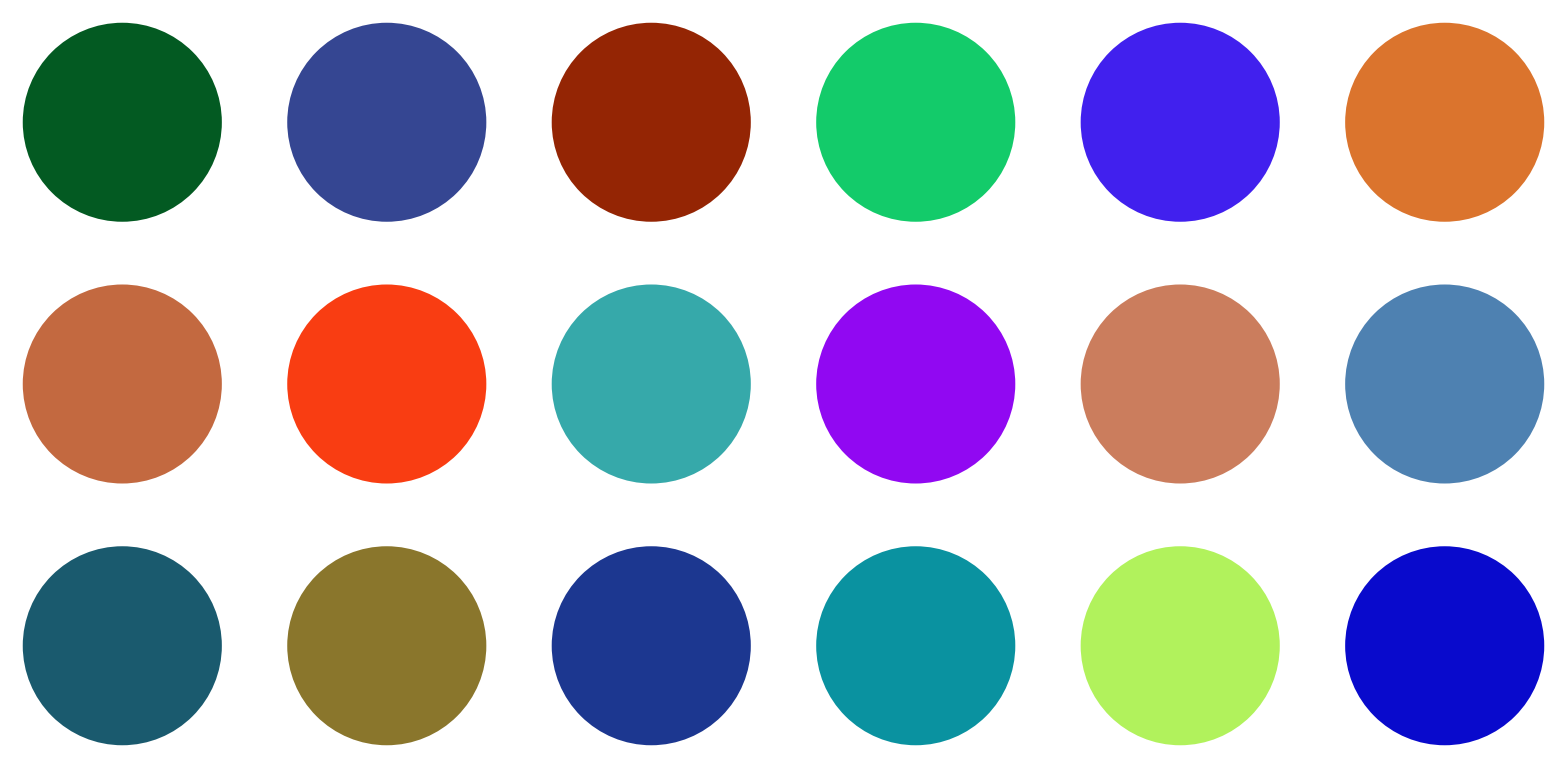

```mathematica
GraphicsGrid@Table[Graphics@Style[Disk[],RandomColor[]],3,6]
```

```mathematica
PieChart@Table[Labeled[a["GDP"],a],{a,EntityList[EntityClass["Country","GroupOf5"]]}]
```

-Graphics-

```mathematica
PieChart[Labeled[#["GDP"],#]&/@EntityClass["Country","GroupOf5"]]
```

PieChart::ldata: EntityClass[Country,GroupOf5] is not a valid dataset or list of datasets.

PieChart[EntityClass[Country[GDP]Country,GroupOf5[GDP]GroupOf5]]

```mathematica
GraphicsGrid[Partition[PieChart[Counts[IntegerDigits[2^#]]]&/@Range[25],5]]
```

-Graphics-

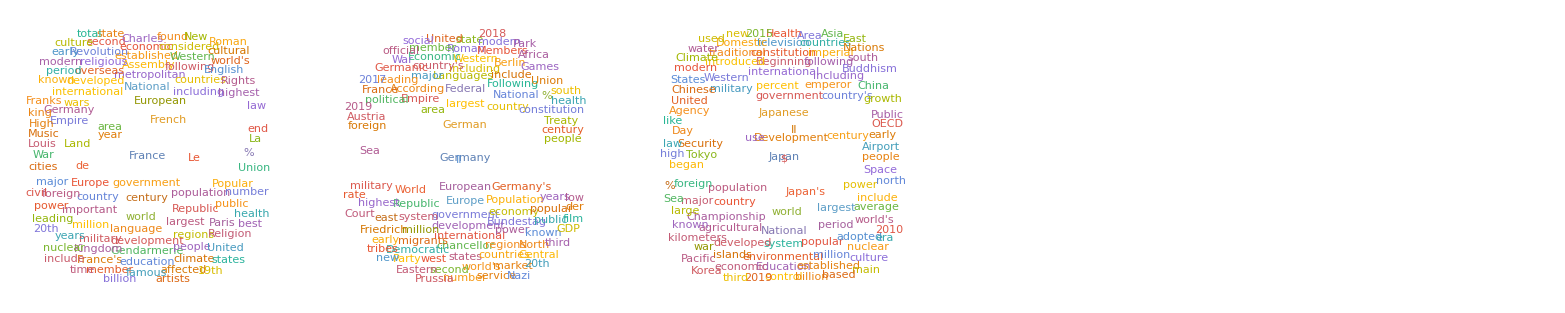

```mathematica
GraphicsRow[WordCloud[WikipediaData[#]]&/@EntityList[EntityClass["Country","GroupOf5"]]]
```

```mathematica
Module[{x=RandomInteger[100,10]},Column[{x,Sort[x],Max[x],Total[x]}]]
```

{42,21,49,79,48,25,2,0,31,36}
{0,2,21,25,31,36,42,48,49,79}
79
333

```mathematica
Module[{x=Entity["Species","Species:GiraffaCamelopardalis"]["Image"]},ImageCollage[{x,Blur[x],EdgeDetect[x],ColorNegate[x]}]]
```

-Graphics-

{1,2,3,4,4,3,2,1,1,2,3,4,4,3,2,1}

```mathematica
NestList[Mod[17#+2,11]&,10,20]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

```mathematica
RandomChoice@Characters["aeiou"]
```

a

```mathematica
Complement[Alphabet[],Characters["aeiou"]]
```

{b,c,d,f,g,h,j,k,l,m,n,p,q,r,s,t,v,w,x,y,z}

```mathematica
Table[StringJoin@Module[{c=Complement[Alphabet[],#],v=#},RandomChoice/@{c,v,c,v,c}]&@Characters["aeiou"],10]
```

{giput,feyim,rugat,sucej,sibis,wowab,biden,dubal,xohub,qubeg}

```mathematica
Module[{a,i},a=0;For[i=1,i≤1000,i++,a=i*(i+1)+a];a]
```

334334000

Product::argmu: Product called with 1 argument; 2 or more arguments are expected.

Product[{1,2,2}]

```mathematica
Table[i*(i+1),{i,1000}]//Total
```

334334000

```mathematica
Nest[1/(1+#)&,x,10]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

```mathematica
Table[{i,j},{i,10},{j,10}]//Flatten
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10}

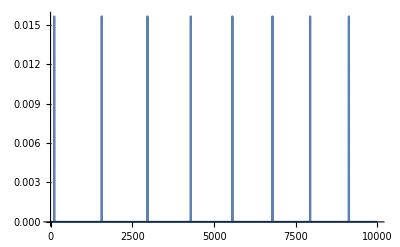

```mathematica
ListLinePlot[Table[First[Timing[Fibonacci[n]]],{n,10000}]]
```

```mathematica
Table[Timing[n^n],{n,10}]
```

{{0.,1},{0.,4},{0.,27},{0.,256},{0.,3125},{0.,46656},{0.,823543},{0.,16777216},{0.,387420489},{0.,10000000000}}

```mathematica
Timing[Nest[3.5 # (1-#)&,1./Pi,10^6]]
```

{0.015625,0.500884}

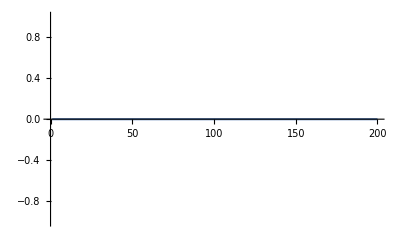

```mathematica
ListLinePlot[Table[First[Timing[Sort[RandomSample[Range[n]]]]],{n,200}]]
```